```mathematica
Quit[]
```

```mathematica
$LoadAddOns={"FeynArts","FeynHelpers"};
Needs["FeynCalc`"]
```

FeynCalc 9.3.1 (stable version). For help, use the documentation center, check out the wiki or visit the forum.

To save your and our time, please check our FAQ for answers to some common FeynCalc questions.

See also the supplied examples. If you use FeynCalc in your research, please cite

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 256 (2020) 107478, arXiv:2001.04407.

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 207 (2016) 432-444, arXiv:1601.01167.

• R. Mertig, M. Böhm, and A. Denner, Comput. Phys. Commun. 64 (1991) 345-359.

FeynArts 3.11 (25 Mar 2022) patched for use with FeynCalc, for documentation see the manual or visit www.feynarts.de.

If you use FeynArts in your research, please cite

• T. Hahn, Comput. Phys. Commun., 140, 418-431, 2001, arXiv:hep-ph/0012260

FeynHelpers 1.3.0, for more information see the accompanying publication.

Have a look at the supplied examples. If you use FeynHelpers in your research, please cite

• V. Shtabovenko, "FeynHelpers: Connecting FeynCalc to FIRE and Package-X", Comput. Phys. Commun., 218, 48-65, 2017, arXiv:1611.06793

Furthermore, remember to cite the authors of the tools that you are calling from FeynHelpers, which are

• FIRE by A. Smirnov, if you are using the function FIREBurn.

• Package-X by H. Patel, if you are using the function PaXEvaluate.

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
CKM = IndexDelta;
Neglect[ME] = Neglect[ME2] = 0;
$FAVerbose=1;
(* use generic model from FeynCalc! The SUNF and SUNT functions in the .mod file have to be replaced by FASUNF and FASUNT *)
SetOptions[InsertFields, Model -> "SMQCD"];
```

```mathematica
processHGG = { V[5],V[5]} -> {S[1]};
tops = CreateTopologies[1, 2->1,  ExcludeTopologies -> {TadpoleCTs,Tadpoles, WFCorrectionCTs,SelfEnergies,SelfEnergyCTs}];
```

```mathematica
allDiags = InsertFields[tops, processHGG,InsertionLevel-> {Particles},ExcludeParticles->{V[1],V[2],V[3],F[3|4,{1|2}],F[4,{3}]}];
```

in total: 2 Particles insertions

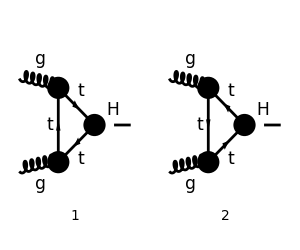

```mathematica
Paint[allDiags,ColumnsXRows->{2,1},PaintLevel->{Particles},ImageSize->{300,250},Numbering->Simple];
```

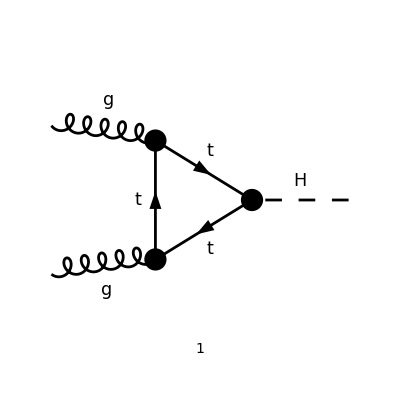

```mathematica
diags=DiagramExtract[allDiags,{1}];
Paint[diags,ColumnsXRows->{2,1},ImageSize->{400,200},Numbering->Simple];
```

```mathematica
(* Set Truncated->True to remove external fields  *)
amp[0]=FCFAConvert[CreateFeynAmp[diags,PreFactor->1,Truncated->True],IncomingMomenta->{p1,p2},OutgoingMomenta->{k},LoopMomenta->{q},List->False,TransversePolarizationVectors->{p1,p2},DropSumOver->True,SMP->True,List->False,LorentzIndexNames-> {μ,ν,σ,ρ},Contract->False,ChangeDimension->D,UndoChiralSplittings->True,FinalSubstitutions-> M$FACouplings]
```

in total: 1 Particles amplitude

(ⅈ tr((γ·(-k+p2+q)+MT).(-(ⅈ yt)/(√2)).(MT+γ·(p2+q)).(-2 ⅈ √π √aS γ^ν T_Col4Col5^Glu2).(MT+γ·q).(-2 ⅈ √π √aS γ^μ T_Col5Col4^Glu1)))/((q^2-MT^2).((p2+q)^2-MT^2).((-k+p2+q)^2-MT^2))

```mathematica
CreateFeynAmp[diags,PreFactor->1,Truncated->False]
```

in total: 1 Particles amplitude

FAFeynAmpList(Process→(V(5,{Glu1}) | p1 | 0 | {√3 ColorCharge}
V(5,{Glu2}) | p2 | 0 | {√3 ColorCharge})→(S(1) | k1 | FCGV(MH) | {}),Model→{SMQCD},GenericModel→{Lorentz},AmplitudeLevel→{Particles},ExcludeParticles→{-F(3,{1,_}),F(3,{1,_}),-F(3,{2,_}),F(3,{2,_}),-F(4,{1,_}),F(4,{1,_}),-F(4,{2,_}),F(4,{2,_}),-F(4,{3,_}),F(4,{3,_}),V(1),V(2),-V(3),V(3)},ExcludeFieldPoints→{},LastSelections→{})(FAFeynAmp(GraphID(Topology==1,Generic==1,Particles==1,Number==1),Integral[q1],ⅈ SumOver(Col4,3) SumOver(Col5,3) SumOver(Glu1,8,External) SumOver(Glu2,8,External) FAFeynAmpDenominator(1/((q1)^2-(FCGV(MT))^2),1/((p2+q1)^2-(FCGV(MT))^2),1/((-k1+p2+q1)^2-(FCGV(MT))^2)) ep(V(5,{Glu1}),p1,Lor1) ep(V(5,{Glu2}),p2,Lor2) tr(gs(-k1+p2+q1)+FCGV(MT),-(ⅈ om_- FCGV(EL) FCGV(MT))/(2 FCGV(MW) FCGV(SW))-(ⅈ om_+ FCGV(EL) FCGV(MT))/(2 FCGV(MW) FCGV(SW)),gs(p2+q1)+FCGV(MT),ⅈ FAGS ga(Lor2).om_- FASUNT(Glu2,Col4,Col5)+ⅈ FAGS ga(Lor2).om_+ FASUNT(Glu2,Col4,Col5),gs(q1)+FCGV(MT),ⅈ FAGS ga(Lor1).om_- FASUNT(Glu1,Col5,Col4)+ⅈ FAGS ga(Lor1).om_+ FASUNT(Glu1,Col5,Col4))))

```mathematica
FCClearScalarProducts[];
ScalarProduct[k,k]=s;
ScalarProduct[k,p1]=s/2;
ScalarProduct[k,p2]=s/2;
ScalarProduct[p1,p1]=0;
ScalarProduct[p2,p2]=0;
ScalarProduct[p1,p2]=s/2;
```

```mathematica
amp[1]=SUNSimplify[FCTraceFactor[amp[0]]]
```

-(2 √2 π aS yt δ^Glu1Glu2 tr((MT-γ·(k-p2-q)).(MT+γ·(p2+q)).γ^ν.(MT+γ·q).γ^μ))/((q^2-MT^2).((p2+q)^2-MT^2).((k-p2-q)^2-MT^2))

```mathematica
PT=MTD[μ,ν]-FVD[p1,μ] FVD[p2,ν]/(s/2) ;(* Apply transverse polarization projector, since the gluons are transverse *)
amp[2]=FullSimplify[DiracSimplify[Contract[PT amp[1]]]]
```

(4 √2 π aS MT yt δ^Glu1Glu2 (s (-2 (D-1) MT^2+2 (D-5) q^2+D s)+4 s (k·q)-8 (p2·q) (s-2 (p1·q))))/(s (q^2-MT^2).((p2+q)^2-MT^2).((k-p2-q)^2-MT^2))

```mathematica
ChangeDimension[amp[2],4]/.{D->4}//Simplify
```

-(8 √2 π aS MT yt δ^Glu1Glu2 (-2 s (k̄·q̄)+s ((q̄)^2+3 MT^2-2 s)+4 (OverBar[p2]·q̄) (s-2 (OverBar[p1]·q̄))))/(s ((q̄)^2-MT^2).((OverBar[p2]+q̄)^2-MT^2).((k̄-OverBar[p2]-q̄)^2-MT^2))

```mathematica
-
```

```mathematica
amp[3]=TID[amp[2],q,ToPaVe->True]//Simplify
```

-4 ⅈ √2 π^3 aS MT yt δ^Glu1Glu2 ((8 MT^2-(D-2) s) C_0(0,0,s,MT^2,MT^2,MT^2)-2 (D-4) B_0(s,MT^2,MT^2))

```mathematica
amp[4]=ChangeDimension[amp[3],4]/.{D->4}//Simplify
```

-8 ⅈ √2 π^3 aS MT yt (4 MT^2-s) δ^Glu1Glu2 C_0(0,0,s,MT^2,MT^2,MT^2)

```mathematica
amp[4]=FullSimplify[PaXEvaluate[amp[3],PaXC0Expand->True,PaXImplicitPrefactor->1/(2 Pi)^(4-2 Epsilon)],Assumptions-> {s>0,MT>0}]
```

-(ⅈ aS MT yt δ^Glu1Glu2 ((4 MT^2-s) log^2((√(s (s-4 MT^2))+2 MT^2-s)/(2 MT^2))+4 s))/(2 √2 π s)

```mathematica
Quit[];
```

```mathematica
Needs["X`"]
```

Package-X v2.1.1, by Hiren H. Patel
For more information, see the

```mathematica
amp[0]=PVC[0,1,0,mc^2, 2 mc^2 + s,mc^2,m,M,M]
```

C_1(mc^2,2 mc^2+s,mc^2;m,M,M)

```mathematica
LoopRefine[amp[0],Part-> UVDivergent]
```

0

```mathematica
amp[1]=LoopRefine[amp[0]]//DiscExpand//FullSimplify
```

-(2 (m^2-M^2+mc^2) C_0(mc^2,mc^2,2 mc^2+s;M,m,M)-(2 λ^(1/2)(m^2,M^2,mc^2) log((λ^(1/2)(m^2,M^2,mc^2)+m^2+M^2-mc^2)/(2 m M)))/mc^2+((m^2-M^2+mc^2) log(m^2/M^2))/mc^2+(2 √((2 mc^2+s) (-4 M^2+2 mc^2+s)) log((√((2 mc^2+s) (-4 M^2+2 mc^2+s))+2 M^2-2 mc^2-s)/(2 M^2)))/(2 mc^2+s))/(2 (2 mc^2-s))

```mathematica
amp[2]=FullSimplify[amp[1]/.{s-> (Subscript[a, s] M)^2,mc-> Subscript[a, c] M,m-> Subscript[a, t] M},Assumptions->{M>0,Subscript[a, s]>0,Subscript[a, c]>0,Subscript[a, t]>0}]
```

-1/(M^2 (2 (a^c)^2-(a^s)^2))((((a^c)^2+(a^t)^2-1) (M^2 (a^c)^2 C_0(M^2 (a^c)^2,M^2 (a^c)^2,M^2 (2 (a^c)^2+(a^s)^2);M,M a^t,M)+log(a^t)))/((a^c)^2)+(λ^(1/2)(M^2,M^2 (a^c)^2,M^2 (a^t)^2) (-log(λ^(1/2)(M^2,M^2 (a^c)^2,M^2 (a^t)^2)+M^2 (-(a^c)^2+(a^t)^2+1))+log(a^t)+2 log(M)+log(2)))/(M^2 (a^c)^2)+√(1-4/(2 (a^c)^2+(a^s)^2)) log(1/2 (√((2 (a^c)^2+(a^s)^2-4) (2 (a^c)^2+(a^s)^2))-2 (a^c)^2-(a^s)^2+2)))

```mathematica
amp0=FullSimplify[Normal[LoopRefineSeries[amp[2],{Subscript[a, s],0,1},{Subscript[a, t],0,1},{Subscript[a, c],0,1}]],Assumptions->{M>0,Subscript[a, s]>0,Subscript[a, c]>0,Subscript[a, t]>0}]
```

7/(12 M^2)

```mathematica
amp1=FullSimplify[Normal[LoopRefineSeries[amp[2],{Subscript[a, s],0,1},{Subscript[a, t],0,1}]],Assumptions->{M>0,Subscript[a, s]>0,Subscript[a, c]>0,Subscript[a, t]>0,Subscript[a, c]<1}]
```

-(M^2 ((a^c)^2-1) (a^c)^2 C_0(M^2 (a^c)^2,M^2 (a^c)^2,2 M^2 (a^c)^2;M,M a^t,M)+√((a^c)^2-2) a^c log(a^c (√((a^c)^2-2)-a^c)+1)+((a^c)^2-1) log(1-(a^c)^2))/(2 M^2 (a^c)^4)